```mathematica
Clear[g]
colList = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
f[x_]:=Log[1+x]
g[x_,x0_,n_]:=(Normal@Series[f[y],{y,x0,n}])/.{y->x}
g[x_]=Normal@Series[f[x],{x,0,2}]
```

x-x^2/2

```mathematica
g[x,0,4]
```

x-x^2/2+x^3/3-x^4/4

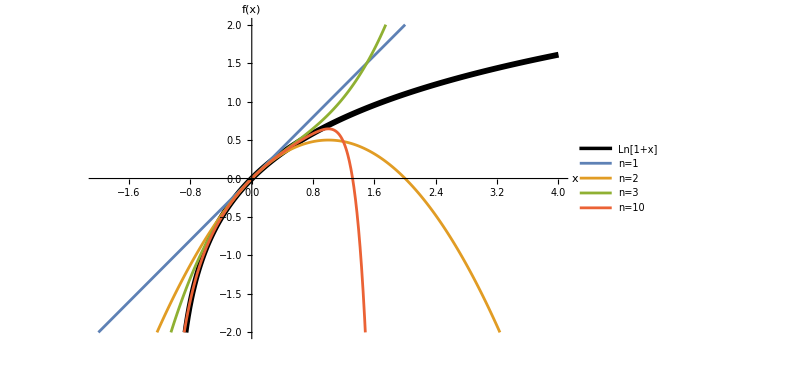

```mathematica
With[{},
Plot[Evaluate@{f[x], 
Sequence@@(g[x,0,#]&/@{1,2,3}), 
g[x,0,10]},{x,-4,4}, AxesOrigin->{0,0}, PlotRange->{{-2,4},{-2,2}}, 
AxesLabel->(Style[#, Black,15]&)/@{"x", "f(x)"}, 
PlotPoints->400,PerformanceGoal->"Quality",
PlotStyle->{{Thickness[0.007], Black}, Sequence@@colList}, 
ImageSize->600, PlotLegends->{"Ln[1+x]", "n=1", "n=2", "n=3", "n=10"}]
]
```